```mathematica
$Assumptions=β>0 && s > 0 && b > 0 && 0<a <= 1 && Element[{u, a, t, x,β,s, ω, ν, b},Reals];
```

### Time

```mathematica
2Exp[a/(2 β)]Sqrt[(4a)/β + 1] Exp[-x a]/Sqrt[2Pi] Exp[(-4 t^2 x)/β-2 I t x]
```

ⅇ^(-a x-2 ⅈ t x+a/(2 β)-(4 t^2 x)/β) √(2/π) √(1+(4 a)/β)

```mathematica
Integrate[%,{x, 1/(2β) , Infinity}, Assumptions -> $Assumptions] // FullSimplify
```

(ⅇ^(-(t (2 t+ⅈ β))/β^2) √(2/π) √(β (4 a+β)))/(4 t^2+a β+2 ⅈ t β)

```mathematica
(ⅇ^(-(4 t^2+a β+2 ⅈ t β)/(2 β^2)) β)/(4 t^2+a β+2 ⅈ t β) /. a->β
```

```mathematica
(ⅇ^(-(4 t^2+2 ⅈ t β+β^2)/(2 β^2)) β)/(4 t^2+2 ⅈ t β+β^2)/.β->10.0 //FullSimplify
```

(1.51633 ⅇ^(((0.-0.1 ⅈ)-0.02 t) t))/(25.+t ((0.+5. ⅈ)+t))

```mathematica
Solve[4 t^2+a β+2 ⅈ t β == 0,t]
```

{{t→1/4 (-ⅈ β-ⅈ √(4 a β+β^2))},{t→1/4 (-ⅈ β+ⅈ √(4 a β+β^2))}}

```mathematica
{{t->1/4 (-ⅈ β-ⅈ √(4 a β+β^2))},{t->1/4 (-ⅈ β+ⅈ √(4 a β+β^2))}}/.{a->3β / 4}//Simplify
```

{{t→-(3 ⅈ β)/4},{t→(ⅈ β)/4}}

### Time with better integration lower bound

```mathematica
2Exp[a/(2 β)]Sqrt[(4a)/β + 1] Exp[-x a]/Sqrt[2Pi] Exp[(-4 t^2 x)/β-2 I t x]
```

ⅇ^(-a x-2 ⅈ t x+a/(2 β)-(4 t^2 x)/β) √(2/π) √(1+(4 a)/β)

```mathematica
Integrate[%,{x, 1/(2β)(1+b) , Infinity}, Assumptions -> $Assumptions] // FullSimplify
```

(ⅇ^(-(4 (1+b) t^2+a b β+2 ⅈ (1+b) t β)/(2 β^2)) √(2/π) √(β (4 a+β)))/(4 t^2+a β+2 ⅈ t β)

```mathematica
FourierTransform[%,t,ω,FourierParameters->{0,-1}, Assumptions->$Assumptions]
```

$Aborted

### Bohr

```mathematica
Exp[a/(2 β)]Sqrt[(4a)/β + 1] Exp[-a x]/Sqrt[2Pi] Sqrt[β/(2x)]Exp[(-(ν + 2x)^2)/(16 x / β)]
```

(ⅇ^(-a x+a/(2 β)-(β (2 x+ν)^2)/(16 x)) √(1+(4 a)/β) √(β/x))/(2 √π)

```mathematica
Integrate[%,{x, 1/(2β) , Infinity}, Assumptions -> $Assumptions] // FullSimplify
```

Piecewise[{{1/2 ⅇ^(a/(2 β)-1/4 (β+√(β (4 a+β))) ν) (Erfc[(√(4 a+β)-β^(3/2) ν)/(2 √2 √β)]+ⅇ^(1/2 √(β (4 a+β)) ν) Erfc[(√(4 a+β)+β^(3/2) ν)/(2 √2 √β)]), ν≠0}, {Indeterminate, True}}]

```mathematica
Limit[1/2 ⅇ^(a/(2 β)-1/4 (β+√(β (4 a+β))) ν) (Erfc[(√(4 a+β)-β^(3/2) ν)/(2 √2 √β)]+ⅇ^(1/2 √(β (4 a+β)) ν) Erfc[(√(4 a+β)+β^(3/2) ν)/(2 √2 √β)]), ν-> 0] // FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

ⅇ^(a/(2 β)) Erfc[(√(1+(4 a)/β))/(2 √2)]

```mathematica
(ⅇ^(-1/4 (β+√(β (4 a+β))) ν) √π (Erfc[(√(4 a+β)-β^(3/2) ν)/(2 √2 √β)]+ⅇ^(1/2 √(β (4 a+β)) ν) Erfc[(√(4 a+β)+β^(3/2) ν)/(2 √2 √β)]))/(√(8 a β+2 β^2))/.a-> β
```

```mathematica
(ⅇ^(-1/4 (β+√5 √(β^2)) ν) √(π/10) (Erfc[(√5 √β-β^(3/2) ν)/(2 √2 √β)]+ⅇ^(1/2 √5 √(β^2) ν) Erfc[(√5 √β+β^(3/2) ν)/(2 √2 √β)]))/(√(β^2))//FullSimplify
```

(ⅇ^(-1/4 (1+√5) β ν) √(π/10) (Erfc[(√5-β ν)/(2 √2)]+ⅇ^(1/2 √5 β ν) Erfc[(√5+β ν)/(2 √2)]))/β

```mathematica
Limit[%, ν-> 0] // FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(√(2 π) Erfc[(√(1+(4 a)/β))/(2 √2)])/(√(β (4 a+β)))

### Bohr with better integration lower bound

```mathematica
Exp[a/(2 β)]Sqrt[(4a)/β + 1] Exp[-a x]/Sqrt[2Pi] Sqrt[β/(2x)]Exp[(-(ν + 2x)^2)/(16 x / β)];
```

```mathematica
Integrate[%,{x, 1/(2β)(1+ε) , Infinity}, Assumptions -> $Assumptions] // FullSimplify
```

Piecewise[{{1/2 ⅇ^(a/(2 β)-1/4 (β+√(β (4 a+β))) ν) (Erfc[(√(4 a+β) (1+ε)-β^(3/2) ν)/(2 √2 √(β (1+ε)))]+ⅇ^(1/2 √(β (4 a+β)) ν) Erfc[(√(4 a+β) (1+ε)+β^(3/2) ν)/(2 √2 √(β (1+ε)))]), ν≠0}, {Indeterminate, True}}]

```mathematica
Exp[a/(2 β)]Sqrt[(4a)/β + 1] Exp[-a x]/Sqrt[2Pi] Sqrt[β/(2x)]Exp[(-(ν + 2x)^2)/(16 x / β)];
```

```mathematica
Limit[%, ν-> 0] // FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(ⅇ^(-a x+a/(2 β)-(x β)/4) √((4 a+β)/x))/(2 √π)

```mathematica
Integrate[%,{x, 1/(2β)(1+ε) , Infinity}, Assumptions -> $Assumptions] // FullSimplify
```

ⅇ^(a/(2 β)) Erfc[(√(((4 a+β) (1+ε))/β))/(2 √2)]

### Energy (integrated by hand!)

```mathematica
β/Sqrt[2Pi](Exp[a/(2 β)]Sqrt[(4a)/β + 1]) Exp[-a x]/Sqrt[2x β - 1] Exp[(-β^2(ω + x)^2)/(2(2x β - 1))]
```

(ⅇ^(-a x β-(β^2 (x+ω)^2)/(2 (-1+2 x β))))/(√(-1+2 x β))

```mathematica
gammaE[ω_, β_, a_] = (Exp[-1/2(a/β + ω β + 1/2)]Exp[-β Abs[ω + 1/(2 β)]Sqrt[a/β + 1/4]])/(2Sqrt[(a/β+1/4)])(Exp[a/(2 β)]Sqrt[(4a)/β + 1]) // FullSimplify
```

ⅇ^(1/4 (-1-2 β ω-2 √(1+(4 a)/β) β Abs[1/(2 β)+ω]))

```mathematica
%/.β-> 10
```

ⅇ^(1/4 (-1-20 ω-20 √(1+(2 a)/5) Abs[1/20+ω]))

```mathematica
Manipulate[
Plot[%, {ω, -0.5, 0.5}],
{a, 0, 10}]
```

### Energy no kink, by hand (ε = 2 is Glauber)

```mathematica
sqAeps = (√((4 a)/β + 1)√(√((β σ^2)/2 b)))/(√8);
sqBeps = β/(√2)Abs[ω + 1/(2 β)]/√(√((β σ^2)/2 b));
(* x0 = √(√((β σ^2)/2 b)); *)
```

```mathematica
gammaEbetter[ω_, β_, σ_, a_, b_] = gammaE[ω, β, a](Erfc[sqAeps- sqBeps] + Exp[4sqAeps sqBeps]Erfc[sqAeps+ sqBeps]) / 2 // FullSimplify
```

1/2 ⅇ^(1/4 (-1-2 β ω-√(1+(4 a)/β) Abs[1+2 β ω])) (ⅇ^(1/2 √(1+(4 a)/β) Abs[1+2 β ω]) Erfc[(√(b (4 a+β) σ^2)+√2 Abs[1+2 β ω])/(2 2^(3/4) (b β σ^2)^(1/4))]+Erfc[(2^(1/4) √(b (4 a+β) σ^2)-2^(3/4) Abs[1+2 β ω])/(4 (b β σ^2)^(1/4))])

```mathematica
D[gammaEbetter[ω, β, σ, a, x0], x0] // FullSimplify
```

-(ⅇ^(1/8 (-2-(x0^2 (4 a+β))/β-4 β ω-(β^2 Abs[1/β+2 ω]^2)/x0^2)) √(1+(4 a)/β))/(√(2 π))

```mathematica
Collect[%, Exp[-(ω β)/2 - 1/4]]
```

-(ⅇ^(-1/4-(x0^2 (4 a+β))/(8 β)-(β ω)/2-(β^2 Abs[1/β+2 ω]^2)/(8 x0^2)) √((4 a+β)/β))/(√(2 π))

```mathematica
Manipulate[Plot[gammaEbetter[ω, β, 1/β, β / 100,1/√(√2)], {ω, -0.7, 0.7}], {β, 1, 20}]  (*b = 10*)
```

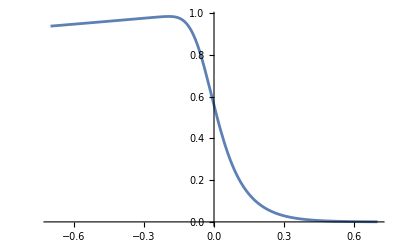

```mathematica
Plot[gammaEbetter[ω, 10, 1/10, 0.1, 2], {ω, -0.7, 0.7}]
```

### Numerical integration check

```mathematica
assumptions=β>0&&b>0&&0<a<=1&&Element[{a,β,ω,Subscript[ν, 1],Subscript[ν, 2],b},Reals];
```

```mathematica
FilterGauss[ω_, ν_, σ_] := Exp[(-(ω - ν)^2)/(4 σ^2)] √(β/(√(2 π)));
gammaE[ω_, β_, a_] = (Exp[-1/2(a/β + ω β + 1/2)]Exp[-β Abs[ω + 1/(2 β)]Sqrt[a/β + 1/4]])/(2Sqrt[(a/β+1/4)])(Exp[a/(2 β)]Sqrt[(4a)/β + 1]) ;
sqAb = (√((4 a)/β + 1)√b)/(√8);
sqBb = β/(√2)Abs[ω + 1/(2 β)]/√b;
gammaEbetter[ω_, β_, σ_, a_, b_] = gammaE[ω, β, a](Erfc[sqAb- sqBb] + Exp[4sqAb sqBb]Erfc[sqAb + sqBb]) / 2;
gamma = gammaEbetter[ω, β, 1/β, a, b ]FilterGauss[ω, Subscript[ν, 1], 1/β] FilterGauss[ω, Subscript[ν, 2], 1/β]
```

1/(4 √(2 π) √(1/4+a/β))ⅇ^(a/(2 β)+1/2 (-1/2-a/β-β ω)-√(1/4+a/β) β Abs[1/(2 β)+ω]-1/4 β^2 (ω-ν_1)^2-1/4 β^2 (ω-ν_2)^2) √(1+(4 a)/β) β (Erfc[(√b √(1+(4 a)/β))/(2 √2)-(β Abs[1/(2 β)+ω])/(√2 √b)]+ⅇ^(√(1+(4 a)/β) β Abs[1/(2 β)+ω]) Erfc[(√b √(1+(4 a)/β))/(2 √2)+(β Abs[1/(2 β)+ω])/(√2 √b)])

```mathematica
1/2 ⅇ^(a/(2 β)-1/4 (β+√(β (4 a+β))) ν) (Erfc[(√(4 a+β) (1+b)-β^(3/2) ν)/(2 √2 √(β (1+b)))]+ⅇ^(1/2 √(β (4 a+β)) ν) Erfc[(√(4 a+β) (1+b)+β^(3/2) ν)/(2 √2 √(β (1+b)))]) /. ν-> Subscript[ν, 1]+Subscript[ν, 2]
```

1/2 ⅇ^(a/(2 β)-1/4 (β+√(β (4 a+β))) (ν_1+ν_2)) (Erfc[((1+b) √(4 a+β)-β^(3/2) (ν_1+ν_2))/(2 √2 √((1+b) β))]+ⅇ^(1/2 √(β (4 a+β)) (ν_1+ν_2)) Erfc[((1+b) √(4 a+β)+β^(3/2) (ν_1+ν_2))/(2 √2 √((1+b) β))])

```mathematica
alpha = % * Exp[-(β^2(Subscript[ν, 1]-Subscript[ν, 2])^2)/8];
```

```mathematica
testCases={
<|a->0.0,β->10.0,b->0.3,Subscript[ν, 1]->0.5,Subscript[ν, 2]->0.2|>,
<|a->0.0,β->10.0,b->0.2,Subscript[ν, 1]->0.5,Subscript[ν, 2]->0.2|>,
<|a->0.0,β->5.0,b->0.7,Subscript[ν, 1]->0.0,Subscript[ν, 2]->0.0|>,
<|a->0.8,β->7.5,b->2.0,Subscript[ν, 1]->0.5,Subscript[ν, 2]->0.5|>,
<|a->0.3,β->10.0,b->0.000001,Subscript[ν, 1]->0.3,Subscript[ν, 2]->-0.5|>
};
```

```mathematica
Do[
currentParams=params;
Print["\nTesting parameters: ",Normal[currentParams]];
(*Substitute parameters into expressions*)gammaNumeric=gamma/. currentParams;
alphaTarget=alpha/. currentParams;
(*Evaluate target alpha numerically*)targetValue=Check[N[alphaTarget,12],$Failed];
If[targetValue===$Failed,Print["Failed to evaluate alpha numerically for these parameters."];Continue[];];
Print["Target alpha value: ",targetValue];
(*Perform numerical integration*)integralValue=Check[NIntegrate[gammaNumeric,{ω,-Infinity,Infinity},WorkingPrecision->12,AccuracyGoal->12],$Failed];(*Added Method->"PrincipalValue" potentially for Abs issues,though defaults might be fine*)If[integralValue===$Failed,Print["NIntegrate failed or gave warnings for these parameters."];Continue[];];
Print["Numerical integral value: ",integralValue];
(*Compare*)diff=Abs[targetValue-integralValue];
Print["Difference: ",diff];
If[diff<10^-8,(*Adjust tolerance as needed based on AccuracyGoal*)Print["Result: Match"];,Print["Result: MISMATCH"];];,
{params,testCases}
]
```

Testing parameters: {a→0.,β→10.,b→0.3,ν_1→0.5,ν_2→0.2}

Target alpha value: 0.009787

Numerical integral value: 0.00978700376789

Difference: 1.32295×10^-12

Result: Match

Testing parameters: {a→0.,β→10.,b→0.2,ν_1→0.5,ν_2→0.2}

Target alpha value: 0.00979343

Numerical integral value: 0.00979342966452

Difference: 4.39358×10^-12

Result: Match

Testing parameters: {a→0.,β→5.,b→0.7,ν_1→0.,ν_2→0.}

Target alpha value: 0.514453

Numerical integral value: 0.514452627474

Difference: 5.59242×10^-10

Result: Match

Testing parameters: {a→0.8,β→7.5,b→2.,ν_1→0.5,ν_2→0.5}

Target alpha value: 0.0160493

Numerical integral value: 0.0160492813027

Difference: 3.40136×10^-9

Result: Match

Testing parameters: {a→0.3,β→10.,b→1.×10^-6,ν_1→0.3,ν_2→-0.5}

Target alpha value: 0.000285432

Numerical integral value: 0.000285431873435

Difference: 6.19635×10^-11

Result: Match

### Chen α^M

```mathematica
alphaMetro[ν1_, ν2_,β_, σ_] = 1/2(Erfc[(β σ^2+(ν1+ν2))/(Sqrt[8]σ)] + Exp[(-β (ν1+ν2))/2]Erfc[(β σ^2-(ν1+ν2))/(Sqrt[8]σ)]) * Exp[(-(ν1-ν2)^2)/(8 σ^2)];
```

```mathematica
p1m = Plot[alphaMetro[ν1, -0.5, 10.0, 1/10.0], {ν1, -1.0, 1.0}];
p2m = Plot[alphaMetro[ν1, 0.0, 10.0, 1/10.0], {ν1, -1.0, 1.0}, PlotStyle->Dashed];
p3m = Plot[alphaMetro[ν1, 0.2, 10.0, 1/10.0], {ν1, -1.0, 1.0}, PlotStyle-> Dotted];
p1mc = Plot[alphaMetro[ν1, -0.5, 20.0, 1/20.0], {ν1, -1.0, 1.0}, PlotRange->All, PlotStyle->Purple];p2mc = Plot[alphaMetro[ν1, 0.0, 20.0, 1/20.0], {ν1, -1.0, 1.0},PlotRange->All,PlotStyle->{Dashed, Purple}];p3mc = Plot[alphaMetro[ν1, 0.2, 20.0, 1/20.0], {ν1, -1.0, 1.0}, PlotRange->All,PlotStyle->{Dotted,Purple}];
```

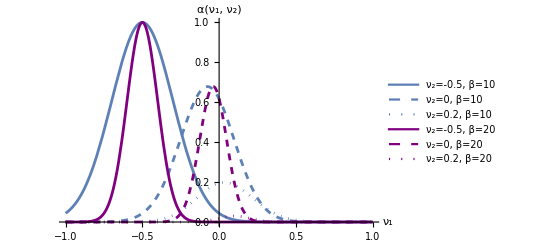

```mathematica
Legended[Show[p1m,p2m, p3m, p1mc, p2mc, p3mc, AxesLabel->{"ν_1","α(ν_1, ν_2)"}],LineLegend[{Directive[RGBColor[0.368,0.498,0.714]],
Directive[RGBColor[0.368,0.498,0.714],Dashed],
Directive[RGBColor[0.368,0.498,0.714],Dotted],
Directive[Purple],
Directive[Purple,Dashed],
Directive[Purple,Dotted]},
{"ν_2=-0.5, β=10","ν_2=0, β=10","ν_2=0.2, β=10",
"ν_2=-0.5, β=20","ν_2=0, β=20","ν_2=0.2, β=20"}]]
```

### Ding et al, Gevrey function

```mathematica
h[t_]:=Exp[-1/(1-t)]/(Exp[-1/(1-t)]+Exp[-1/t]);
bump[x_]:=Piecewise[{{1,Abs[x]<=1/2},{h[2 Abs[x]-1],1/2<Abs[x]<1},{0,Abs[x]>=1}}];
```

```mathematica
Plot[bump[x/2],{x,-3,3},PlotRange->All,PlotLabel->"Bump Function"];
```

```mathematica
alphaGevrey[ν1_,ν2_, β_, S_] := Exp[-1/4(Sqrt[1 + β^2 ν1^2] + Sqrt[1 + β^2 ν2^2] + β(ν1 + ν2))]bump[ν1 / S]bump[ν2 / S];
```

```mathematica
p1 = Plot[alphaGevrey[ν1,-0.5, 10.0, 1], {ν1, -1.0, 1.0}];
p2 = Plot[alphaGevrey[ν1,-0.0, 10.0, 1], {ν1, -1.0, 1.0}, PlotStyle->Dashed];
p3 = Plot[alphaGevrey[ν1,0.2, 10.0, 1], {ν1, -1.0, 1.0}, PlotStyle-> Dotted];
p1c = Plot[alphaGevrey[ν1,-0.5, 20.0, 1], {ν1, -1.0, 1.0}, PlotStyle-> {Purple}];
p2c = Plot[alphaGevrey[ν1,0.0, 20.0, 1], {ν1, -1.0, 1.0}, PlotStyle-> {Dashed, Purple}];
p3c = Plot[alphaGevrey[ν1,0.2, 20.0, 1], {ν1, -1.0, 1.0}, PlotStyle-> {Dotted, Purple}];
```

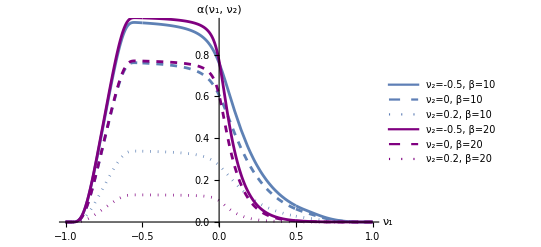

```mathematica
Legended[Show[p1,p2, p3, p1c, p2c, p3c, AxesLabel->{"ν_1","α(ν_1, ν_2)"}],LineLegend[{Directive[RGBColor[0.368,0.498,0.714]],
Directive[RGBColor[0.368,0.498,0.714],Dashed],
Directive[RGBColor[0.368,0.498,0.714],Dotted],
Directive[Purple],
Directive[Purple,Dashed],
Directive[Purple,Dotted]},
{"ν_2=-0.5, β=10","ν_2=0, β=10","ν_2=0.2, β=10",
"ν_2=-0.5, β=20","ν_2=0, β=20","ν_2=0.2, β=20"}]]
```

### Ding α but where S∝ 1/β

```mathematica
p1s = Plot[alphaGevrey[ν1,-0.5, 10.0, 5/10], {ν1, -0.5, 0.5}];
p2s = Plot[alphaGevrey[ν1,-0.0, 10.0, 5/10], {ν1, -0.5, 0.5}, PlotStyle->Dashed];
p3s = Plot[alphaGevrey[ν1,0.2, 10.0, 5/10], {ν1, -0.5, 0.5}, PlotStyle-> Dotted];
p1cs = Plot[alphaGevrey[ν1,-0.5, 20.0, 5/20], {ν1, -0.5, 0.5}, PlotStyle-> {Purple}];
p2cs = Plot[alphaGevrey[ν1,0.0, 20.0, 5/20], {ν1, -0.5, 0.5}, PlotStyle-> {Dashed, Purple}];
p3cs = Plot[alphaGevrey[ν1,0.2, 20.0, 5/20], {ν1, -0.5, 0.5}, PlotStyle-> {Dotted, Purple}];
```

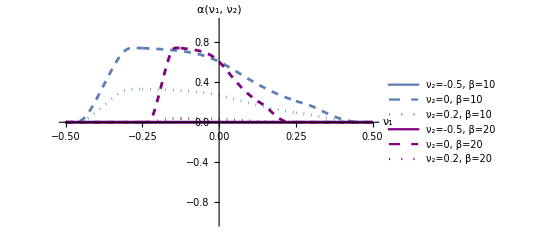

```mathematica
Legended[Show[p1s,p2s, p3s, p1cs, p2cs, p3cs, AxesLabel->{"ν_1","α(ν_1, ν_2)"}],LineLegend[{Directive[RGBColor[0.368,0.498,0.714]],
Directive[RGBColor[0.368,0.498,0.714],Dashed],
Directive[RGBColor[0.368,0.498,0.714],Dotted],
Directive[Purple],
Directive[Purple,Dashed],
Directive[Purple,Dotted]},
{"ν_2=-0.5, β=10","ν_2=0, β=10","ν_2=0.2, β=10",
"ν_2=-0.5, β=20","ν_2=0, β=20","ν_2=0.2, β=20"}]]
```

### The kink in the Metro like result that makes energy integral have a mid quadrature error

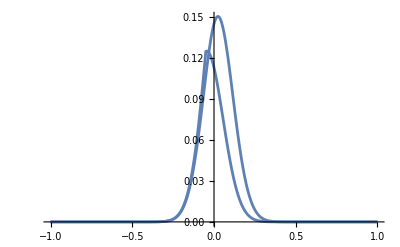

```mathematica
GammaGevrey[ω_, β_] := Exp[-1/4(Sqrt[1 + β^2 ω^2]+ β ω)];
GammaMetro[ω_, β_]:=Exp[-β ((ω + 1/(2β))+Abs[(ω + 1/(2β))])/2];
GammaSmooth[ω_, β_]:=1/(1+Exp[β ω]);
FilterGauss[ω_, ν_, σ_] := Exp[(-(ω - ν)^2)/(4 σ^2)] √(β/(√(2 π)));
pgev = Plot[GammaGevrey[ω, 10]FilterGauss[ω, -0.12,1/10]FilterGauss[ω, 0.23, 1/10], {ω, -1.0, 1.0 }, PlotRange->All];
pmet = Plot[GammaMetro[ω, 10]FilterGauss[ω, -0.12,1/10]FilterGauss[ω, 0.23, 1/10], {ω, -1.0, 1.0 }, PlotRange->All];
Show[pgev, pmet]
```

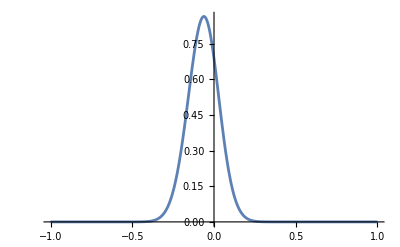

```mathematica
Plot[GammaGevrey[ω, 10]FilterGauss[ω, -0.05,1/10]FilterGauss[ω, -0.05, 1/10], {ω, -1.0, 1.0 }, PlotRange->All]
```

### Failed attempts at finding a different γ(ω) that keeps skew-symmetry too.

```mathematica
$Assumptions=0< β && σ > 0  && -0.5 <=Subscript[ν, 1]<=0.5 && -0.5 <=Subscript[ν, 2]<=0.5&&Element[{β,ω, σ, Subscript[ν, 1], Subscript[ν, 2]},Reals];
```

```mathematica
GammaGevrey[ω, β]FilterGauss[ω, Subscript[ν, 1], 1/β]FilterGauss[ω, Subscript[ν, 2], 1/β]
```

ⅇ^(1/4 (-β ω-√(1+β^2 ω^2))-1/4 β^2 (ω-ν_1)^2-1/4 β^2 (ω-ν_2)^2)

```mathematica
Integrate[%, {ω, -Infinity, Infinity}, Assumptions->$Assumptions]
```

Integrate[ⅇ^(1/4 (-β ω-√(1+β^2 ω^2))-1/4 β^2 (ω-ν_1)^2-1/4 β^2 (ω-ν_2)^2),{ω,-∞,∞},Assumptions→0<β<100&&σ>0&&-0.5≤ν_1≤0.5&&-0.5≤ν_2≤0.5 ((β|ω|σ|ν_1|ν_2)∈ℝ)]

```mathematica
GammaSmooth[ω, β]FilterGauss[ω, Subscript[ν, 1],σ]FilterGauss[ω, Subscript[ν, 2], σ]
```

(ⅇ^(-(ω-ν_1)^2/(4 σ^2)-(ω-ν_2)^2/(4 σ^2)))/(1+ⅇ^(β ω))

```mathematica
Integrate[%, {ω, -Infinity, Infinity}, Assumptions->$Assumptions]
```

TerminatedEvaluation[RecursionLimit]

### Getting rid of the kink by starting linear combination by ε higher.

```mathematica
$Assumptions=β>0 && s > 0 && ε>0 && 0<a <= 1 && Element[{u, a, t, x,β,s, ω, ν, ε, s},Reals];
```

```mathematica
Exp[-a x]/Sqrt[2x β - 1] Exp[(-β^2(ω + x)^2)/(2(2x β - 1))]
```

(ⅇ^(-a x-(β^2 (x+ω)^2)/(2 (-1+2 x β))))/(√(-1+2 x β))

```mathematica
Integrate[%,{x, 1/(2β) , Infinity}, Assumptions -> $Assumptions] // FullSimplify
```

Integrate[(ⅇ^(-a x-(β^2 (x+ω)^2)/(-2+4 x β)))/(√(-1+2 x β)),{x,1/(2 β),∞},Assumptions→True]

### Quick Fourier check

```mathematica
f[t_, β_]:= Exp[-t^2 / β^2] √((√(2 / π))/β);
F=FourierTransform[f[t,β],t,ω,FourierParameters->{0,-1}, Assumptions->$Assumptions]
```

(ⅇ^(-1/4 β^2 ω^2) √(1/β))/((2 π)^(1/4) √(1/β^2))

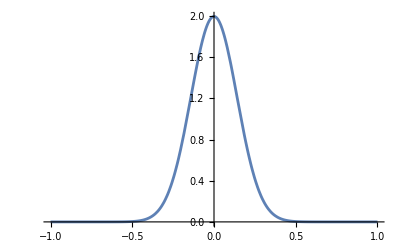

```mathematica
Plot[F /.β->10, {ω, -1.0, 1.0}]
```

```mathematica
Integrate[Abs[f[t, 10]]^2, {t, -Infinity, Infinity}]
```

1

```mathematica
F /. β-> 10
```

```mathematica
√5 ⅇ^(-25 ω^2) (2/π)^(1/4)
```

```mathematica
√5 ⅇ^(-25 ω^2) (2/π)^(1/4)
```

√5 ⅇ^(-25 ω^2) (2/π)^(1/4)

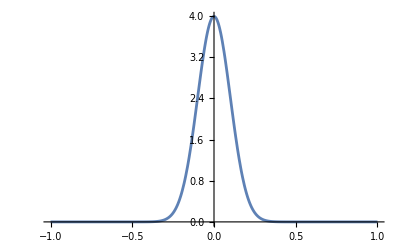

```mathematica
Plot[Abs[%]^2, {ω, -1.0, 1.0}, PlotRange->All]
```

```mathematica
Integrate[Abs[%]^2, {ω, -Infinity, Infinity}]
```

1